```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

## Library ComplexMatrixDraw (copy to your Notebook, evaluate and use the complexMatrixDraw function)

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{Append[center+{-0.5,-0.5},0],Append[center+{0.5,-0.5},0],Append[center+{0.5,0.5},0],Append[center+{-0.5,0.5},0]}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[Append[center,0]]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[Append[center-OptionValue[barDiameter]{0.5,0.5},0],Append[center+OptionValue[barDiameter]{0.5,0.5},val]],
_,Cylinder[{Append[center,0],Append[center,val]},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{Append[center,val],Append[center,val]+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

## Some utility functions (evaluate)

makeColVect transform a list of numbers {n1, n2, n3}  into a column vector  { {n1}, {n2}, {n3}}.
ρToVect "columnizes" a density matrix column by column 
{{ρ11, ρ12, ρ13, ρ14},{ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44} }==>{ {ρ11}, {ρ21}, {ρ31}, {ρ41}, {ρ12}, {ρ22}, {ρ32}, {ρ42}, {ρ13},{ ρ23}, {ρ33}, {ρ43}, {ρ14}, {ρ24}, {ρ34}, {ρ44} }

```mathematica
Remove[myCompareGraph]
```

```mathematica
makeColVect[xList_]:={#}&/@xList;

ρToVect=Composition[ makeColVect,Flatten,Transpose];

decomposeInBase[v_, vList_]:=LinearSolve[Flatten/@vList//Transpose,Flatten[v]];

fidDensity[ρ1_,ρ2_]=Chop[Tr[MatrixPower[Chop[MatrixPower[ρ1,1/2].ρ2.MatrixPower[ρ1,1/2]],1/2]]];
fidChi[χ1_,χRef_]=Chop[Tr[χ1.χRef]];

myOpts1={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False};
myCompareGraph[mList_,colorList_:{Red,Blue,RGBColor[0,0.5,0], Magenta},fid_:"None"]:=
Block[{label=Switch[fid,"None","",_,"F12="<>ToString[Round[100ToExpression[fid][mList[[1]],mList[[2]]]]/100.]]},
Show[
MapIndexed[complexMatrixDraw[#1,myOpts1~Join~{borderDirectives->{colorList[[Mod[#2[[1]],Length[colorList],1]]]},arrowDirectives->{Arrowheads[0],colorList[[Mod[#2[[1]],Length[colorList],1]]]}}]&,mList,{1}]
,PlotLabel->label]
];
```

```mathematica
myOpts2={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False,borderDirectives->{Red},arrowDirectives->{Arrowheads[0],Red}};
```

## Definitions of the ideal states, density matrices, operator basis and β matrix (evaluate)

### States and density matrices for process map

We define:
base1={ |0>, |1>}as the single qubit state basis
base2={|00>,|01>,|10>,|11>}={|0>, |1>, |2>, |3>} as the two qubit state basis
stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 as the set of states used to map the process.
Then we built the ρListIn, the list of density matrices  corresponding to stateSet2  (expressed in base2). Note that ρListIn is a base for the 4x4 density matrices.

For superoperator formalism, density matrices are "columnized" column by column: {ρ11, ρ21, ρ31, ρ41, ρ12, ρ22, ρ32, ρ42, ρ13, ρ23, ρ33, ρ43, ρ14, ρ24, ρ34, ρ44 }.
we also define a simpler (but non physical) basis for density matrices:
ρBase2 = the 16  4x4 density matrices with all elements equal to 0 except one equal to 1 (in the order ρ11=1, ρ21=1, ... so that the index of the matrix corresponds to that of element 1 in the corresponding columnized vector).

```mathematica
Clear[k0,k1,kPlus,kMinus];
stateBase1Name={"0","1"};
stateSet1Name={"0","1","+","-"};
ketBase1={k0,k1};
ketSet1={k0,k1,kPlus,kMinus};
```

```mathematica
stateBase2Name=Outer[#1<>#2&,stateBase1Name,stateBase1Name]//Flatten;
stateSet2Name=Outer[#1<>#2&,stateSet1Name,stateSet1Name]//Flatten;
ketBase2=Outer[KroneckerProduct,ketBase1,ketBase1]//Flatten;
ketSet2=Outer[KroneckerProduct,ketSet1,ketSet1]//Flatten;
```

```mathematica
k0={1,0}//makeColVect;
k1={0,1}//makeColVect;
kPlus={1,1}/Sqrt[2]//makeColVect;
kMinus={1,+ⅈ}/Sqrt[2]//makeColVect;
```

```mathematica
ρBase2=Transpose/@MapIndexed[Partition[ReplacePart[#1,#2[[1]]->1],4]&,ConstantArray[0,{16,16}]];
```

```mathematica
ketSet1=ketSet1;
ketSet2=ketSet2;
braSet1=ConjugateTranspose /@ ketSet1;
braSet2=ConjugateTranspose /@ ketSet2;
ρListIn=MapThread[Dot,{ketSet2,braSet2}];
```

```mathematica
Print["stateBase2Name=\n",stateBase2Name]
Print["ketBase2=\n",MatrixForm/@ketBase2]
Print["ketSet2=\n",MatrixForm/@ketSet2]
Print["ρListIn=\n",MatrixForm/@ρListIn]
Print["ρBase2=\n",MatrixForm/@ρBase2]
Print["columnized ρBase2=\n",MatrixForm/@(ρToVect/@ρBase2)]
```

stateBase2Name=
{00,01,10,11}

ketBase2=
{(1
0
0
0),(0
1
0
0),(0
0
1
0),(0
0
0
1)}

ketSet2=
{(1
0
0
0),(0
1
0
0),(1/(√2)
1/(√2)
0
0),(1/(√2)
ⅈ/(√2)
0
0),(0
0
1
0),(0
0
0
1),(0
0
1/(√2)
1/(√2)),(0
0
1/(√2)
ⅈ/(√2)),(1/(√2)
0
1/(√2)
0),(0
1/(√2)
0
1/(√2)),(1/2
1/2
1/2
1/2),(1/2
ⅈ/2
1/2
ⅈ/2),(1/(√2)
0
ⅈ/(√2)
0),(0
1/(√2)
0
ⅈ/(√2)),(1/2
1/2
ⅈ/2
ⅈ/2),(1/2
ⅈ/2
ⅈ/2
-1/2)}

ρListIn=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | 1/2 | 0 | 0
1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/2 | 0 | 0
ⅈ/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 1/2 | 1/2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | -ⅈ/2
0 | 0 | ⅈ/2 | 1/2),(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2),(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4
1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4),(1/2 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 1/2),(1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | -ⅈ/4 | -1/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
-1/4 | ⅈ/4 | ⅈ/4 | 1/4)}

ρBase2=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

columnized ρBase2=
{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1)}

### Operators on states

We choose the Pauli bases for the operators, with a minor change: σy is replaced by i σy to get real numbers everywhere.
So we get
opBase1={I=Identity, X=σx, Y=i σy, Z=σz} as the operator basis for a single qubit
opBase2 = opBase1 x opBase1 for the operator basis on two qubits.

```mathematica
opBase1Name={"I","X","Y","Z"};
Clear[id,σx,iσy,σz];
opBase1={id,σx,iσy,σz};
opBase2Name=Outer[StringJoin,opBase1Name,opBase1Name]//Flatten;
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1=opBase1;
opBase2=opBase2;
```

```mathematica
σx1=KroneckerProduct[σx,id];
σy1=KroneckerProduct[σy,id];
σz1=KroneckerProduct[σz,id];
σx2=KroneckerProduct[id,σx];
σy2=KroneckerProduct[id,σy];
σz2=KroneckerProduct[id,σz];
```

```mathematica
Print["opBase1Names=\n",MatrixForm/@opBase1Name]
Print["opBase1=\n",MatrixForm/@opBase1]
Print["opBase2Names=\n",MatrixForm/@opBase2Name]
Print["opbase2=\n",MatrixForm/@opBase2]
```

opBase1Names=
{I,X,Y,Z}

opBase1=
{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | 1
-1 | 0),(1 | 0
0 | -1)}

opBase2Names=
{II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ}

opbase2=
{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

## Lindblad with relaxation - λ Process (evaluate)

-Graphics-

### calculation

We define the two qubit density matrix and its columnized form

```mathematica
(ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}})//MatrixForm;
(ρVec=ρ//Transpose//Flatten)//MatrixForm;
ρFromρVec=(Partition[#,4]//Transpose)&;
ρVecFromρ=(#//Transpose//Flatten)&;
```

We define the hamiltonian (g and Δ=ω2-ω1 are angular frequencies = energies divided by hbar ) and check that the corresponding unitary evolution is the ideal one (defined everywhere in this notebook).

```mathematica
(hSW[g_,Δ_]=1/2{{0,0,0,0},{0,Δ,g,0},{0,g,-Δ,0},{0,0,0,0}})//MatrixForm
(hMatrix[g_,Δ_]=CoefficientArrays[Flatten[Transpose[hSW[g,Δ].ρ-ρ.hSW[g,Δ]]],ρVec][[2]]//Normal)//MatrixForm;
(uS2=MatrixExp[-I hSW[g,0] 2π/4/g]//FullSimplify)//MatrixForm
uS2==uS
hMatrix[g,Δ]//MatrixForm
```

(0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0
0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

{{1,0,0,0},{0,1/(√2),-ⅈ/(√2),0},{0,-ⅈ/(√2),1/(√2),0},{0,0,0,1}}==uS

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | g/2 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | g/2 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | g/2 | -Δ | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ | g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | g/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
σp = {{0, 0}, {1, 0}};
σm = {{0,1}, {0, 0}}; 
σm1=KroneckerProduct[σm,id];
σm2=KroneckerProduct[id,σm];
c1r=√Γr1 σm1;
c2r=√Γr2 σm2;
c1ϕ=√(Γϕ1/2)σz1;
c2ϕ=√(Γϕ2/2)σz2;
(MatrixForm/@{c1r,c2r,c1ϕ,c2ϕ})//Row
```

(0 | 0 | √Γr1 | 0
0 | 0 | 0 | √Γr1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(0 | √Γr2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | √Γr2
0 | 0 | 0 | 0)((√Γϕ1)/(√2) | 0 | 0 | 0
0 | (√Γϕ1)/(√2) | 0 | 0
0 | 0 | -(√Γϕ1)/(√2) | 0
0 | 0 | 0 | -(√Γϕ1)/(√2))((√Γϕ2)/(√2) | 0 | 0 | 0
0 | -(√Γϕ2)/(√2) | 0 | 0
0 | 0 | (√Γϕ2)/(√2) | 0
0 | 0 | 0 | -(√Γϕ2)/(√2))

-Graphics-

```mathematica
assumptions={Γr1>0,Γr2>0,Γϕ1>0,Γϕ2>0};
liouv[s_]:=Block[{sds=ConjugateTranspose[s].s},Simplify[s.ρ.ConjugateTranspose[s]-1/2(ρ.sds+sds.ρ),assumptions]];
l=(Plus @@(liouv/@{c1r,c2r,c1ϕ,c2ϕ}))//FullSimplify//Transpose//Flatten;
mRel=CoefficientArrays[l,ρVec][[2]]//Normal;
Plus@@(mRel.ρVec-l//FullSimplify)==0
mRelax[Γr1_,Γr2_,Γϕ1_,Γϕ2_]=mRel;
Print["Relaxation superoperator = "];
mRel//MatrixForm
```

True

Relaxation superoperator =

(0 | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0
0 | 0 | 0 | 0 | 0 | -Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1 | 0 | 0 | 0 | 0 | Γr2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1-Γr2)

```mathematica
(mSqSw[g_,Δ_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=MatrixExp[(-ⅈ hMatrix[g,Δ] + mRelax[Γr1,Γr2,Γϕ1,Γϕ2]) tSW]//Chop)//MatrixForm;
```

In addition, we add an error evolution operator U and superoperator M that corresponds to X, Y and Z errors occuring before or after the target operation

```mathematica
uError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ];
uErrorT[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=ConjugateTranspose[uError[X1,X2,Y1,Y2,Z1,Z2]];
mError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:=CoefficientArrays[Flatten[Transpose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ].ρ.ConjugateTranspose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ]]]],ρVec][[2]]//Normal
```

```mathematica
λProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=mError[X1,X2,Y1,Y2,Z1,Z2].mSqSw[g,Δ,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcess[{g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_}]:=λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcessNum[list_/;And@@NumberQ/@list]:=λProcess[list];
```

### Plots

```mathematica
λP0=λProcess[{2π.0083,0,0,0,0,0,0,0,.043 2π.0083,.036 2π.0083,0,0,t}]//Chop;
λP0b=λProcess[{2π.0083,0,0,0,0,0,0,0,.043 2π.0083,.036 2π.0083,.02 2π.0083,.02 2π.0083,t}]//Chop;
λP0c=λProcess[{2π.0083,0,0,0,0,0,2π 0.122 t,0,.043 2π.0083,.036 2π.0083,.02 2π.0083,.02 2π.0083,t}]//Chop;
```

```mathematica
(ρVec2=ρVecFromρ[ρListIn[[2]]])//MatrixForm;
ρFromρVec[ρVec2]//MatrixForm;
ρVec2Prim[t_]=ρFromρVec[λP0.ρVec2];
ρVec2Primb[t_]=ρFromρVec[λP0b.ρVec2];
ρVec2Primc[t_]=ρFromρVec[λP0c.ρVec2];
```

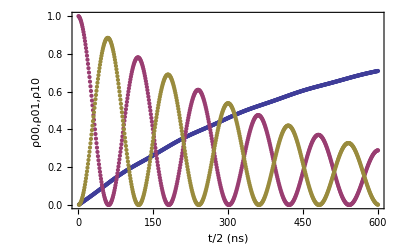

```mathematica
ta1=Table[ρVec2Prim[t],{t,0,600}];
ρ00List1=#[[1,1]]&/@ta1;
ρ01List1=#[[2,2]]&/@ta1;
ρ10List1=#[[3,3]]&/@ta1;
gr1=ListPlot[{ρ00List1,ρ01List1,ρ10List1},Frame->True,FrameLabel->{"t/2 (ns)","ρ00,ρ01,ρ10"}]
ρGraphList0=complexMatrixDraw[#1,myOpts1]&/@ta1;
ListAnimate[ρGraphList0]
```

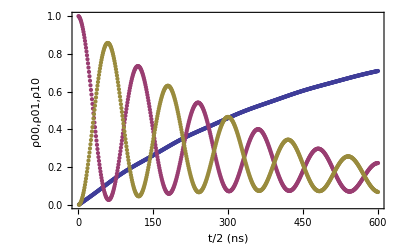

```mathematica
ta1c=Table[ρVec2Primc[t],{t,0,600}];
ρ00List1c=#[[1,1]]&/@ta1c;
ρ01List1c=#[[2,2]]&/@ta1c;
ρ10List1c=#[[3,3]]&/@ta1c;
gr1c=ListPlot[{ρ00List1c,ρ01List1c,ρ10List1c},Frame->True,FrameLabel->{"t/2 (ns)","ρ00,ρ01,ρ10"}]
ρGraphList0c=complexMatrixDraw[#1,myOpts1]&/@ta1c;
ListAnimate[ρGraphList0c]
```

## Import Data

Directory : [Lab computer]\Labo\local - expdata\FO - C5 \3rd - Run \2011_ 02 _ 09\film of swapPauli Set : State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26 - 0 _ 0 _Swap of state 0 _ 0 _ 180 _ 0 - 0 _ 0 _Measured spins - 300 _ 0. txt
Density Matrices : State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26 - 0 _ 0 _Swap of state 0 _ 0 _ 180 _ 0 - 0 _ 0 _Measured spins - 300 _ 0 _Density Matrices - 300 _ 0. txt

### Import Pauli sets and recalculate non physical ρListExp3 = { ρInListExp3, ρOutListExp3 } ρ's and physical ρ's ρListExp3P = { ρInListExp3P, ρOutListExp3P }

#### define the operators and showPauliSet function

```mathematica
opBase1NameA={"i","x","y","z"};
Clear[id,σx,σy,σz,iσy];
opBase1A={id,σx,σy,σz};
opBase2NameA=Outer[StringJoin,opBase1NameA,opBase1NameA]//Flatten
opBase2A=Outer[KroneckerProduct,opBase1A,opBase1A]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1A=opBase1A;
opBase2A=opBase2A;
MatrixForm/@opBase2A
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

```mathematica
ticks={Transpose[{Range[16],ToUpperCase/@opBase2NameA}],{-1,-0.5,0,0.5,1}};
showPauliSet[pauliSetlist_,opts___]:=ListPlot[pauliSetlist,Frame->True,PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Medium]},{RGBColor[0,0.5,0]},{Magenta}},PlotRange->{{0.5,16.5},{-1.05,1.05}},FrameTicks->ticks,opts]
```

#### import pauli sets

We import the measured Pauli sets (readout errors corrected) and reorder each Pauli set according to the opBase2Names order

```mathematica
pauliSets=Import["L:\\local-expdata\\FO-C5\\3rd-Run\\2011_02_09\\film of swap\\State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26-0_0_Swap of state 0_0_180_0-0_0_Measured spins-300_0.txt","Table"];
pauliSets[[1]]
set=Rest[pauliSets[[1]]]
orderOp=Position[set,#]&/@opBase2NameA//Flatten
times=Rest[Transpose[pauliSets][[1]]]
pauliSets=Rest[pauliSets];
pauliSets=(Rest[#]&/@pauliSets);
reorderPauliSet[ps_]:=ps[[#]]&/@orderOp;
pauliSets=reorderPauliSet/@pauliSets;
Dimensions[pauliSets]
opBase2NameA
```

{t,xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{16,13,14,15,4,1,2,3,8,5,6,7,12,9,10,11}

{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.,22.,24.,26.,28.,30.,32.,34.,36.,38.,40.,42.,44.,46.,48.,50.,52.,54.,56.,58.,60.,62.,64.,66.,68.,70.,72.,74.,76.,78.,80.,82.,84.,86.,88.,90.,92.,94.,96.,98.,100.,102.,104.,106.,108.,110.,112.,114.,116.,118.,120.,122.,124.,126.,128.,130.,132.,134.,136.,138.,140.,142.,144.,146.,148.,150.,152.,154.,156.,158.,160.,162.,164.,166.,168.,170.,172.,174.,176.,178.,180.,182.,184.,186.,188.,190.,192.,194.,196.,198.,200.,202.,204.,206.,208.,210.,212.,214.,216.,218.,220.,222.,224.,226.,228.,230.,232.,234.,236.,238.,240.,242.,244.,246.,248.,250.,252.,254.,256.,258.,260.,262.,264.,266.,268.,270.,272.,274.,276.,278.,280.,282.,284.,286.,288.,290.,292.,294.,296.,298.,300.,302.,304.,306.,308.,310.,312.,314.,316.,318.,320.,322.,324.,326.,328.,330.,332.,334.,336.,338.,340.,342.,344.,346.,348.,350.,352.,354.,356.,358.,360.,362.,364.,366.,368.,370.,372.,374.,376.,378.,380.,382.,384.,386.,388.,390.,392.,394.,396.,398.,400.,402.,404.,406.,408.,410.,412.,414.,416.,418.,420.,422.,424.,426.,428.,430.,432.,434.,436.,438.,440.,442.,444.,446.,448.,450.,452.,454.,456.,458.,460.,462.,464.,466.,468.,470.,472.,474.,476.,478.,480.,482.,484.,486.,488.,490.,492.,494.,496.,498.,500.,502.,504.,506.,508.,510.,512.,514.,516.,518.,520.,522.,524.,526.,528.,530.,532.,534.,536.,538.,540.,542.,544.,546.,548.,550.,552.,554.,556.,558.,560.,562.,564.,566.,568.,570.,572.,574.,576.,578.,580.,582.,584.,586.,588.,590.,592.,594.,596.,598.}

{300,16}

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

Let's plot them.

```mathematica
pauliGraphList=MapThread[showPauliSet[{#1},PlotLabel->"t="<>ToString[#2]<>"ns"]&,{pauliSets,times}];
ListAnimate[pauliGraphList]
```

#### from Pauli sets to density matrices and vice and versa

Now we calculate the expectation values of the Pauli operators < Pi > = Tr(ρ.Pi) as a function of ρ: {<Pi>}=A.ρ

```mathematica
ρM1={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
(ρV1=Transpose[ρM1]//Flatten)//MatrixForm
(meanValues=Tr[ρM1.#]&/@opBase2A)//MatrixForm
(matA=CoefficientArrays[meanValues,ρV1]//Normal//#[[2]]&)//MatrixForm
pauliSetFromρ=matA.Flatten[Transpose[#]]&;
(matAInv=Inverse[matA])//MatrixForm
```

(ρ11
ρ21
ρ31
ρ41
ρ12
ρ22
ρ32
ρ42
ρ13
ρ23
ρ33
ρ43
ρ14
ρ24
ρ34
ρ44)

(ρ11+ρ22+ρ33+ρ44
ρ12+ρ21+ρ34+ρ43
ⅈ ρ12-ⅈ ρ21+ⅈ ρ34-ⅈ ρ43
ρ11-ρ22+ρ33-ρ44
ρ13+ρ24+ρ31+ρ42
ρ14+ρ23+ρ32+ρ41
ⅈ ρ14-ⅈ ρ23+ⅈ ρ32-ⅈ ρ41
ρ13-ρ24+ρ31-ρ42
ⅈ ρ13+ⅈ ρ24-ⅈ ρ31-ⅈ ρ42
ⅈ ρ14+ⅈ ρ23-ⅈ ρ32-ⅈ ρ41
-ρ14+ρ23+ρ32-ρ41
ⅈ ρ13-ⅈ ρ24-ⅈ ρ31+ⅈ ρ42
ρ11+ρ22-ρ33-ρ44
ρ12+ρ21-ρ34-ρ43
ⅈ ρ12-ⅈ ρ21-ⅈ ρ34+ⅈ ρ43
ρ11-ρ22-ρ33+ρ44)

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1)

(1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | -1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | -ⅈ/4 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 1/4)

Finally we calculate the density matrices ρ by linear inversion  ρ = A^-1{<Pi>}...

```mathematica
ρFromPauliSet=Chop[Transpose[Partition[matAInv.#,4]]]&;
ρs=ρFromPauliSet/@pauliSets;
ρs//Dimensions
```

{300,4,4}

```mathematica
ρGraphList=myCompareGraph[{#1}]&/@ρs;
ListAnimate[ρGraphList]
```

#### To physical matrices

Although these ρ's are Hermitian and have a trace 1, they are non physical because they are not positive (all eigenvalues positive)

```mathematica
Min[Chop[Eigenvalues[#]]]&/@ρs
```

{-0.0295575,-0.0855606,-0.108316,-0.107907,-0.107794,-0.122722,-0.11963,-0.114432,-0.124035,-0.127077,-0.122224,-0.136407,-0.132868,-0.117266,-0.123548,-0.100411,-0.116548,-0.0870841,-0.0829693,-0.0802901,-0.0478385,-0.0545548,-0.0347272,-0.0455309,-0.0262288,-0.0258917,-0.0235158,-0.0212395,-0.0222796,-0.0261575,-0.0282312,-0.0166212,-0.0244298,-0.0263504,-0.0522563,-0.0456854,-0.0394193,-0.058943,-0.0460224,-0.0509798,-0.0565863,-0.0642944,-0.0730226,-0.0651126,-0.0747534,-0.0902917,-0.067208,-0.0657618,-0.058829,-0.0774054,-0.0589147,-0.061309,-0.0528652,-0.0479884,-0.0535854,-0.0427805,-0.0518016,-0.0503032,-0.0615913,-0.067496,-0.0629913,-0.0700659,-0.0707496,-0.0673755,-0.0507185,-0.067272,-0.0602433,-0.0626136,-0.0530575,-0.0576946,-0.047698,-0.04336,-0.0318088,-0.034628,-0.0225782,-0.025896,-0.0296411,-0.0207195,-0.0203674,-0.0172493,-0.0196341,-0.0168993,-0.0138019,-0.0160133,-0.016742,-0.0222308,-0.0223101,-0.0223742,-0.0357454,-0.0251824,-0.0311216,-0.0289616,-0.0366497,-0.0358591,-0.0365231,-0.0427431,-0.04755,-0.0475358,-0.0420629,-0.0484406,-0.0362203,-0.0380571,-0.030501,-0.0216624,-0.0227562,-0.0247398,-0.0232933,-0.0301468,-0.0316106,-0.0257567,-0.018673,-0.0257533,-0.0318167,-0.0302502,-0.0345355,-0.038348,-0.032833,-0.0325468,-0.0403972,-0.0368201,-0.036642,-0.0334915,-0.0266823,-0.0262982,-0.0260089,-0.0271122,-0.0252766,-0.0241811,-0.0176797,-0.0153417,-0.0106919,-0.00797656,-0.0111887,-0.0154167,-0.0129617,-0.0163596,-0.00888023,-0.0119317,-0.0154538,-0.0188125,-0.0125915,-0.0138997,-0.0160502,-0.0190385,-0.0224032,-0.0276832,-0.0199565,-0.0289822,-0.0211851,-0.0200436,-0.0161489,-0.0200756,-0.0113619,-0.0174606,-0.0185847,-0.0168937,-0.017094,-0.0214156,-0.0154163,-0.018206,-0.0187113,-0.0154669,-0.0141716,-0.013884,-0.0204741,-0.0183728,-0.0282781,-0.0181558,-0.0180685,-0.0192932,-0.0171573,-0.0158207,-0.0233676,-0.0158012,-0.010972,-0.011467,-0.0153487,-0.0144325,-0.0211009,-0.0127511,-0.0175844,-0.0140837,-0.0127942,-0.00798348,-0.0116421,-0.00894892,-0.012106,-0.00915787,-0.00598795,-0.0114452,-0.0125581,-0.016294,-0.00705061,-0.00925504,-0.0107222,-0.00939818,-0.00986043,-0.0100735,-0.0157473,-0.0121737,-0.0132935,-0.00964859,-0.0145187,-0.0109127,-0.0120562,-0.0108065,-0.0137422,-0.00789075,-0.0122301,-0.0121645,-0.00729261,-0.0147958,-0.0121288,-0.00938829,-0.00611158,-0.0123337,-0.0135456,-0.0113883,-0.00860858,-0.0108457,-0.011988,-0.012694,-0.0122603,-0.0188554,-0.0147761,-0.0130287,-0.0154935,-0.00892719,-0.0110809,-0.0127178,-0.0162302,-0.0149452,-0.018975,-0.0148293,-0.0137732,-0.0104434,-0.00432491,-0.0079284,-0.00955722,-0.00185263,-0.0103322,-0.00457932,-0.0089056,-0.00756009,-0.0033288,-0.00745211,-0.00852648,-0.00575197,-0.00309017,-0.00460445,-0.00693744,-0.00514751,-0.00701376,-0.00630334,-0.00495251,-0.00387868,-0.0106682,-0.00632677,-0.012593,-0.00707405,-0.00603371,-0.00622402,-0.00320641,-0.000661106,-0.00602166,-0.0116655,-0.00625257,-0.0110386,-0.00836058,-0.008236,-0.00841774,-0.00642984,-0.00625782,-0.00615181,-0.0118985,-0.0120545,-0.0113263,-0.00986051,-0.0108653,-0.00914837,-0.0120034,-0.00841578,-0.0127066,-0.00444534,-0.00904793,-0.00781646,-0.00537113,-0.00955351,-0.0127199,-0.0104689,-0.0102272,-0.00814567,-0.00503722,-0.00888772,-0.00946009,-0.00937713,-0.00872133,-0.00176574,-0.00532007,-0.00334119}

Let us make them physical by minimization of the distance ( Hilbert-Schmitt norm) between each non physical matrices and physical matrices

```mathematica
Remove[d2Num,ρPofρ,ρM2,ρRealL,bestρPofρ]
```

```mathematica
d2Num[m1_/;And @@ (NumberQ/@Flatten[m1]),m2_/;And @@ (NumberQ/@Flatten[m2])]:=Plus@@(m2-m1//Flatten//Chop//Abs//#^2&)
```

```mathematica
ρPofρ[ρ_/;And @@ (NumberQ/@Flatten[ρ])]:=Block[{val,vec},
{val,vec}=Eigensystem[ρ]//Chop[#,10^-6]&//Transpose//Sort//Reverse//Transpose;
val=Max[#,0]&/@val;val=val/Plus@@val;
Chop[Transpose[vec].DiagonalMatrix[val].Conjugate[vec],10^-6]
];
```

```mathematica
ρM2=Table[ρ0[i,j],{i,1,4},{j,1,4}];
ρRealL=MapIndexed[Take[#1,#2[[1]]]&,ρM2,1]//Flatten;
(ρM2=ρM2//.{ρ0[i_,j_]/;j>i->Conjugate[ρ0[j,i]],ρ0[i_,j_]/;j<i->reρ0[i,j]+I imρ0[i,j]}//ComplexExpand)//MatrixForm
ρRealL=ρRealL/.ρ0[i_,j_]/;j≠i->Sequence[reρ0[i,j],imρ0[i,j]]//ComplexExpand
```

(ρ0[1,1] | -ⅈ imρ0[2,1]+reρ0[2,1] | -ⅈ imρ0[3,1]+reρ0[3,1] | -ⅈ imρ0[4,1]+reρ0[4,1]
ⅈ imρ0[2,1]+reρ0[2,1] | ρ0[2,2] | -ⅈ imρ0[3,2]+reρ0[3,2] | -ⅈ imρ0[4,2]+reρ0[4,2]
ⅈ imρ0[3,1]+reρ0[3,1] | ⅈ imρ0[3,2]+reρ0[3,2] | ρ0[3,3] | -ⅈ imρ0[4,3]+reρ0[4,3]
ⅈ imρ0[4,1]+reρ0[4,1] | ⅈ imρ0[4,2]+reρ0[4,2] | ⅈ imρ0[4,3]+reρ0[4,3] | ρ0[4,4])

{ρ0[1,1],reρ0[2,1],imρ0[2,1],ρ0[2,2],reρ0[3,1],imρ0[3,1],reρ0[3,2],imρ0[3,2],ρ0[3,3],reρ0[4,1],imρ0[4,1],reρ0[4,2],imρ0[4,2],reρ0[4,3],imρ0[4,3],ρ0[4,4]}

```mathematica
ρRealLofρ[ρm_]=ρRealL/.{ρ0[i_,j_]->ρm[[i,j]],reρ0[i_,j_]->Re[ρm[[i,j]]],imρ0[i_,j_]->Im[ρm[[i,j]]]}
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partd: Part specification ρm ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρm ⟦ 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{ρm⟦1,1⟧,Re[ρm⟦2,1⟧],Im[ρm⟦2,1⟧],ρm⟦2,2⟧,Re[ρm⟦3,1⟧],Im[ρm⟦3,1⟧],Re[ρm⟦3,2⟧],Im[ρm⟦3,2⟧],ρm⟦3,3⟧,Re[ρm⟦4,1⟧],Im[ρm⟦4,1⟧],Re[ρm⟦4,2⟧],Im[ρm⟦4,2⟧],Re[ρm⟦4,3⟧],Im[ρm⟦4,3⟧],ρm⟦4,4⟧}

```mathematica
ρofρRealL[ρReal_]=ρM2/.{
ρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,ρ0[i,j]]][[-1]]]],
reρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,reρ0[i,j]]][[-1]]]],
imρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,imρ0[i,j]]][[-1]]]]}
```

Part::partd: Part specification ρReal ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{{ρReal⟦1⟧,ρReal⟦2⟧-ⅈ ρReal⟦3⟧,ρReal⟦5⟧-ⅈ ρReal⟦6⟧,ρReal⟦10⟧-ⅈ ρReal⟦11⟧},{ρReal⟦2⟧+ⅈ ρReal⟦3⟧,ρReal⟦4⟧,ρReal⟦7⟧-ⅈ ρReal⟦8⟧,ρReal⟦12⟧-ⅈ ρReal⟦13⟧},{ρReal⟦5⟧+ⅈ ρReal⟦6⟧,ρReal⟦7⟧+ⅈ ρReal⟦8⟧,ρReal⟦9⟧,ρReal⟦14⟧-ⅈ ρReal⟦15⟧},{ρReal⟦10⟧+ⅈ ρReal⟦11⟧,ρReal⟦12⟧+ⅈ ρReal⟦13⟧,ρReal⟦14⟧+ⅈ ρReal⟦15⟧,ρReal⟦16⟧}}

```mathematica
bestρPofρ[ρm_/;And @@ (NumberQ/@Flatten[ρm]),showProgress_:False]:=Block[{a=If[showProgress,Print["Start minimization"]],sol=FindMinimum[d=d2Num[ρPofρ[ρofρRealL[ρRealL]],ρm],Evaluate[Transpose[{ρRealL,ρRealLofρ[ρm]}]],StepMonitor:>If[showProgress,Print[d],None]]},ρPofρ[ρofρRealL[ρRealL/.sol[[2]]]]]
```

```mathematica
FindMinimum[d=d2Num[ρPofρ[ρofρRealL[ρRealL]],ρs[[1]]],Evaluate[Transpose[{ρRealL,ρRealLofρ[ρs[[1]]]}]],StepMonitor:>If[showProgress,Print[d],None]]
```

```mathematica
ρsP=bestρPofρ/@ρs;
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

General::stop: Further output of Flatten will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

Now the ρ's are physical:

```mathematica
Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρsP]
Map[Tr,ρsP]//Chop
Map[Min[Chop[Eigenvalues[#]]]&,ρsP]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ρGraphListP=myCompareGraph[{#}]&/@ρsP;
ListAnimate[ρGraphListP]
```

#### analysis of the systematic preparation and tomographic pulse errors

```mathematica
ticks={Transpose[{Range[16],ToUpperCase/@opBase2NameA}],{-1,-0.5,0,0.5,1}};
showPauliSet[pauliSetlist_]:=ListPlot[pauliSetlist,Frame->True,PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Medium]},{RGBColor[0,0.5,0]}},PlotRange->{{0.5,16.5},{-1.05,1.05}},FrameTicks->ticks]
```

Despite fidelities close to 1, we notice large spurious matrix elements in the input ρ's. So we suspect large pulse errors, which we try to determine.

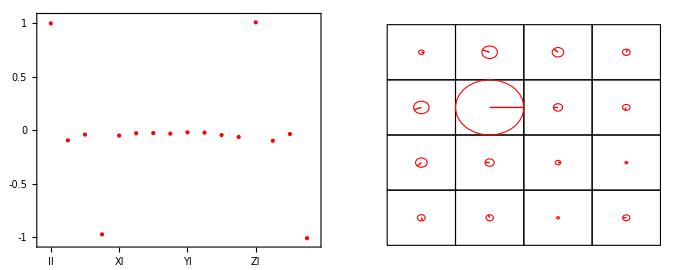

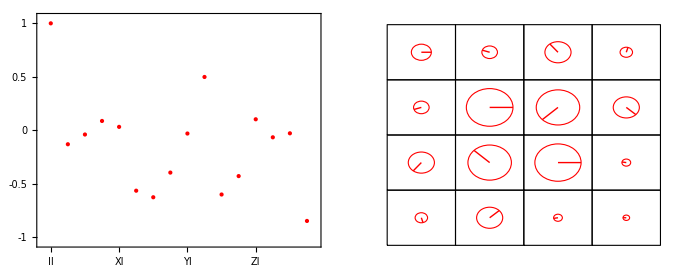

```mathematica
GraphicsRow[{showPauliSet[pauliSets[[1]]],myCompareGraph[{ρs[[1]]}]}]
GraphicsRow[{showPauliSet[pauliSets[[16]]],myCompareGraph[{ρs[[16]]}]}]
```

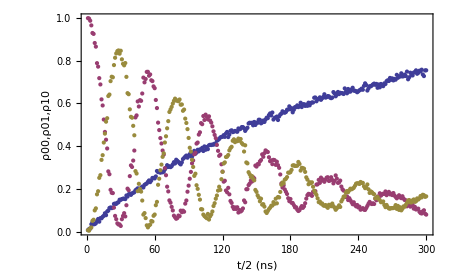

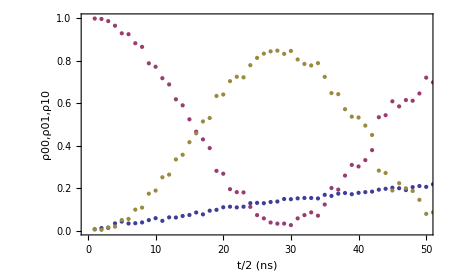

```mathematica
ρ00List=#[[1,1]]&/@ρs;
ρ01List=#[[2,2]]&/@ρs;
ρ10List=#[[3,3]]&/@ρs;
gr0=ListPlot[{ρ00List,ρ01List,ρ10List},Frame->True,FrameLabel->{"t/2 (ns)","ρ00,ρ01,ρ10"}]
Show[%,PlotRange->{{0,50},{0,1}}]
```

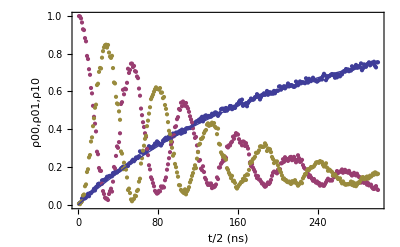

```mathematica
Show[gr0,Plot[1-Exp[-t/215],{t,0,300}]]
```

```mathematica
opBase2NameA
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

We assume the following systematic errors:  
	- " π rotation" around of  π+ϵπx  with different ϵπx for qubit 1 and 2;
	- " π/2 rotation" of  π/2 + ϵhπ with different ϵhπ for qubit 1 and 2  and for x and y axis ;
	- y axis making 90°+ θy with x axis, with different θy for qubit 1 and 2;
	- x-y frame at tomography rotated by θt with respect to x-y frame at preparation,  with different θt for qubit 1 and 2.
As a consequence :	
	- instead of preparing the states of setState1 we prepare other states with errors
	-instead of measuring the expectation values of  opBase1, we measure those of opBase1E with errors

Instead of preparing  single qubit states stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 and corresponding density matrices ρListIn, we actually prepare ρListInE.
We check that ρListInE=ρListIn when all errors are zeroed.

```mathematica
Clear[id,rx1,ry1,rx2,ry2]
opSet1E1={id,rx1[π],ry1[π/2],rx1[-π/2]};
opSet1E2={id,rx2[π],ry2[π/2],rx2[-π/2]};
opE2=Outer[KroneckerProduct,opSet1E1,opSet1E2]//Flatten;
id={{1,0},{0,1}};
rx1[π]=MatrixExp[- I (π+ϵπx1Prep)/2 σx];
rx2[π]=MatrixExp[- I (π+ϵπx2Prep)/2 σx];
rx1[-π/2]=MatrixExp[ I( π/2+ϵhπx1Prep)/2 σx];
rx2[-π/2]=MatrixExp[ I( π/2+ϵhπx2Prep)/2 σx];
ry1[π/2]=MatrixExp[- I( π/2+ϵhπy1Prep)/2 (Cos[θy1]σy-Sin[θy1]σx)];
ry2[π/2]=MatrixExp[- I (π/2+ϵhπy2Prep)/2 (Cos[θy2]σy-Sin[θy2]σx)];
opE2=opE2;
ρListInE=#.ρListIn[[1]].ConjugateTranspose[#]&/@opE2//FullSimplify//ComplexExpand//FullSimplify;
noErrorRule={ϵπx1Prep->0,ϵπx2Prep->0,ϵhπx1Prep->0, ϵhπx2Prep->0,ϵhπy1Prep->0, ϵhπy2Prep->0,θy1->0,θy2->0};
ρListInNoE=ρListInE/.noErrorRule;
(ρListIn-ρListInNoE//Flatten//Max)==0
"ρListInE="
MatrixForm/@ρListInE
```

True

ρListInE=

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[ϵπx2Prep] | 0 | 0
1/2 ⅈ Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 (1-Sin[ϵhπy2Prep]) | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] | 0 | 0
1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] | 1/2 (1+Sin[ϵhπy2Prep]) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Cos[1/4 (π+2 ϵhπx2Prep)]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] | 0 | 0
1/2 ⅈ Cos[ϵhπx2Prep] | Sin[1/4 (π+2 ϵhπx2Prep)]^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Sin[ϵπx1Prep/2]^2 | 0 | -1/2 ⅈ Sin[ϵπx1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅈ Sin[ϵπx1Prep] | 0 | Cos[ϵπx1Prep/2]^2 | 0
0 | 0 | 0 | 0),(Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | -1/2 ⅈ Sin[ϵπx1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep]
1/2 ⅈ Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep/2]^2 | 1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep]
1/2 ⅈ Sin[ϵπx1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep]
-1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | 1/2 ⅈ Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep] | 1/2 ⅈ Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | Cos[ϵπx1Prep/2]^2 Cos[ϵπx2Prep/2]^2),(-1/2 (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep/2]^2 | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | -1/4 ⅈ ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep]
1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep/2]^2 | 1/2 (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep/2]^2 | 1/4 Cos[ϵhπy2Prep] Sin[ϵπx1Prep] (-ⅈ Cos[θy2]+Sin[θy2]) | -1/4 ⅈ (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep]
-1/4 ⅈ (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | 1/4 Cos[ϵhπy2Prep] Sin[ϵπx1Prep] (ⅈ Cos[θy2]+Sin[θy2]) | -1/2 Cos[ϵπx1Prep/2]^2 (-1+Sin[ϵhπy2Prep]) | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Cos[ϵπx1Prep/2]^2
1/4 ⅈ ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep] | 1/4 ⅈ (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | 1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Cos[ϵπx1Prep/2]^2 | 1/4 (1+Cos[ϵπx1Prep]) (1+Sin[ϵhπy2Prep])),(Cos[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep/2]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] Sin[ϵπx1Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπx2Prep]) Sin[ϵπx1Prep] | -1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep]
1/2 ⅈ Cos[ϵhπx2Prep] Sin[ϵπx1Prep/2]^2 | Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep/2]^2 | 1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | -1/2 ⅈ Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep]
-1/4 ⅈ (-1+Sin[ϵhπx2Prep]) Sin[ϵπx1Prep] | 1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | Cos[1/4 (π+2 ϵhπx2Prep)]^2 Cos[ϵπx1Prep/2]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] Cos[ϵπx1Prep/2]^2
-1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | 1/2 ⅈ Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep] | 1/2 ⅈ Cos[ϵhπx2Prep] Cos[ϵπx1Prep/2]^2 | Cos[ϵπx1Prep/2]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2),(1/2 (1-Sin[ϵhπy1Prep]) | 0 | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] | 0 | 1/2 (1+Sin[ϵhπy1Prep]) | 0
0 | 0 | 0 | 0),(-1/2 (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 ⅈ ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep]
-1/4 ⅈ (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | -1/2 Cos[ϵπx2Prep/2]^2 (-1+Sin[ϵhπy1Prep]) | 1/4 Cos[ϵhπy1Prep] Sin[ϵπx2Prep] (ⅈ Cos[θy1]+Sin[θy1]) | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Cos[ϵπx2Prep/2]^2
1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπy1Prep] Sin[ϵπx2Prep] (-ⅈ Cos[θy1]+Sin[θy1]) | 1/2 (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep/2]^2 | -1/4 ⅈ (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep]
1/4 ⅈ ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep] | 1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Cos[ϵπx2Prep/2]^2 | 1/4 ⅈ (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | 1/4 (1+Cos[ϵπx2Prep]) (1+Sin[ϵhπy1Prep])),(1/4 (-1+Sin[ϵhπy1Prep]) (-1+Sin[ϵhπy2Prep]) | -1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] (Cos[θy1+θy2]-ⅈ Sin[θy1+θy2])
-1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 (-1+Sin[ϵhπy1Prep]) (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ (θy1-θy2)) Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] | 1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπy2Prep])
-1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ (θy1-θy2)) Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] | -1/4 (1+Sin[ϵhπy1Prep]) (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπy1Prep])
1/4 Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] (Cos[θy1+θy2]+ⅈ Sin[θy1+θy2]) | 1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπy1Prep]) | 1/4 (1+Sin[ϵhπy1Prep]) (1+Sin[ϵhπy2Prep])),(1/4 (-1+Sin[ϵhπx2Prep]) (-1+Sin[ϵhπy1Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπx2Prep]) | -1/4 ⅈ ⅇ^(-ⅈ θy1) Cos[ϵhπx2Prep] Cos[ϵhπy1Prep]
-1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 (1+Sin[ϵhπx2Prep]) (-1+Sin[ϵhπy1Prep]) | 1/4 Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] (ⅈ Cos[θy1]+Sin[θy1]) | 1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπx2Prep])
-1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπx2Prep]) | 1/4 Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] (-ⅈ Cos[θy1]+Sin[θy1]) | -1/4 (-1+Sin[ϵhπx2Prep]) (1+Sin[ϵhπy1Prep]) | -1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπy1Prep])
1/4 ⅈ ⅇ^(ⅈ θy1) Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] | 1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπx2Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπy1Prep]) | 1/4 (1+Sin[ϵhπx2Prep]) (1+Sin[ϵhπy1Prep])),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 | 0 | -1/2 ⅈ Cos[ϵhπx1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅈ Cos[ϵhπx1Prep] | 0 | Sin[1/4 (π+2 ϵhπx1Prep)]^2 | 0
0 | 0 | 0 | 0),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπx1Prep]) Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵhπx1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep]
-1/4 ⅈ (-1+Sin[ϵhπx1Prep]) Sin[ϵπx2Prep] | Cos[1/4 (π+2 ϵhπx1Prep)]^2 Cos[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵhπx1Prep] Cos[ϵπx2Prep/2]^2
1/2 ⅈ Cos[ϵhπx1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep]
-1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | 1/2 ⅈ Cos[ϵhπx1Prep] Cos[ϵπx2Prep/2]^2 | 1/2 ⅈ Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 Sin[1/4 (π+2 ϵhπx1Prep)]^2),(1/4 (-1+Sin[ϵhπx1Prep]) (-1+Sin[ϵhπy2Prep]) | -1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπx1Prep]) | 1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπy2Prep]) | -1/4 ⅈ ⅇ^(-ⅈ θy2) Cos[ϵhπx1Prep] Cos[ϵhπy2Prep]
-1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπx1Prep]) | -1/4 (-1+Sin[ϵhπx1Prep]) (1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] (-ⅈ Cos[θy2]+Sin[θy2]) | -1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπy2Prep])
-1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] (ⅈ Cos[θy2]+Sin[θy2]) | -1/4 (1+Sin[ϵhπx1Prep]) (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπx1Prep])
1/4 ⅈ ⅇ^(ⅈ θy2) Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] | 1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπx1Prep]) | 1/4 (1+Sin[ϵhπx1Prep]) (1+Sin[ϵhπy2Prep])),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 Cos[1/4 (π+2 ϵhπx2Prep)]^2 | 1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπx1Prep]) | 1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπx2Prep]) | -1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep]
-1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπx1Prep]) | Cos[1/4 (π+2 ϵhπx1Prep)]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2 | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | -1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπx2Prep])
-1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπx2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | Cos[1/4 (π+2 ϵhπx2Prep)]^2 Sin[1/4 (π+2 ϵhπx1Prep)]^2 | -1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπx1Prep])
-1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | 1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπx2Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπx1Prep]) | Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2)}

- instead of measuring i,x,y,z, we measure i,xp,yp,z with up=Rudagger Z Ru and Ru the rotation (with errors) trying to bring u along z.
The list of  measured operators is opE2b instead of opBase2.

```mathematica
Clear[id,xe1,ye1,xe2,ye2,σz,iye1,iye2];
opE1b1={id,xe1,ye1,σz};
opE1b2={id,xe2,ye2,σz};
opE2b=Outer[KroneckerProduct,opE1b1,opE1b2]//Flatten;
opE1b1I={id,xe1,iye1,σz};
opE1b2I={id,xe2,iye2,σz};
opE2bI=Outer[KroneckerProduct,opE1b1I,opE1b2I]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
rx1[π/2]=MatrixExp[ -I (π/2+ϵhπx1Tomo)/2 (Cos[θt1]σx+Sin[θt1]σy)];
rx2[π/2]=MatrixExp[- I (π/2+ϵhπx2Tomo)/2(Cos[θt2]σx+Sin[θt2]σy)];
ry1[-π/2]=MatrixExp[ I (π/2+ϵhπy1Tomo)/2 (Cos[θy1+θt1]σy-Sin[θy1+θt1]σx)];
ry2[-π/2]=MatrixExp[I (π/2+ϵhπy2Tomo)/2 (Cos[θy2+θt2]σy-Sin[θy2+θt2]σx)];
xe1=ConjugateTranspose[ry1[-π/2]].σz.ry1[-π/2]//ComplexExpand//Simplify;
ye1= ConjugateTranspose[rx1[π/2]].σz.rx1[π/2]//ComplexExpand//Simplify;
xe2=ConjugateTranspose[ry2[-π/2]].σz.ry2[-π/2]//ComplexExpand//Simplify;
ye2= ConjugateTranspose[rx2[π/2]].σz.rx2[π/2]//ComplexExpand//Simplify;
iye1=I ye1;
iye2=I ye2;
noErrorRule=noErrorRule~Join~{ϵhπx1Tomo->0,ϵhπx2Tomo->0,ϵhπy1Tomo->0,ϵhπy2Tomo->0,θt1->0,θt2->0};
opE2b=opE2b//FullSimplify;
opE2bI=opE2bI//FullSimplify;
opNoEI=opE2bI/.noErrorRule;
(opNoEI-opBase2//Flatten//Max)==0
Print ["opE2b="]
MatrixForm/@opE2b
```

True

opE2b=

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
0 | 0 | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
0 | 0 | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | -Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo]),(Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]-ⅈ Sin[θt1+θt2+θy1+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]+ⅈ Sin[θt1+θt2+θy1+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1])
Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo]),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | -Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | -Sin[ϵhπy1Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | -Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | ⅇ^(-ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (-Cos[θt1+θt2]+ⅈ Sin[θt1+θt2])
Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅇ^(-ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
-Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (Cos[θt1+θt2]+ⅈ Sin[θt1+θt2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] | Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (ⅈ Cos[θt1]+Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | 0 | -Sin[ϵhπx1Tomo]),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2])
0 | 0 | -Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (ⅈ Cos[θt2]+Sin[θt2])
0 | 0 | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

The measured Pauli sets {Tr[ρE.PauliE]} contain both preparation and tomography pulse errors

```mathematica
pauliSetError[ρMi_]:=Tr[ρMi.#]&/@opE2b
pauliSetInErrorL=pauliSetError/@ρListInE;
```

```mathematica
params={ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2};
params0=ConstantArray[0,Length[params]];
paramRule[paramsNum_]:=MapThread[#1->#2&,{params,paramsNum}]
```

We start with state |01>

```mathematica
ρStartExp=ρs[[1]];
pauliSetStartExp=pauliSets[[1]];
ρStopExp=ρs[[16]];
pauliSetStopExp=pauliSets[[16]];
ρStartCalc=ρListInE[[2]];
pauliSetStartCalc=pauliSetInErrorL[[2]];
```

```mathematica
pauliSetStartCalc/.paramRule[params0]
```

{1,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,-1}

```mathematica
GraphicsRow[{showPauliSet[{pauliSetStartExp,pauliSetStartCalc/.paramRule[params0]}],myCompareGraph[{ρStartExp,ρStartCalc/.paramRule[params0]}]}]
```

-Graphics-

and apply the gate keeping only Z1, Z2 and ϵ as gate error parameters

```mathematica
ρStopCalc[{Z1_,Z2_,ϵ_}]:=(λProcessNum[{1,0,0,0,0,0,Z1,Z2,0.043,0.036,0.02,0.02,1/2. π (1+ϵ)}].(ρStartCalc//Transpose//Flatten))//Partition[#,4]&//Transpose//Chop
pauliSetStopCalc[{Z1_,Z2_,ϵ_}]:=pauliSetFromρ[ρStopCalc[{Z1,Z2,ϵ}]]//Chop
apparentPauliSetStopCalc[{Z1_,Z2_,ϵ_}]:=pauliSetError[ρStopCalc[{Z1,Z2,ϵ}]]//Chop
apparentρStopCalc[{Z1_,Z2_,ϵ_}]:=ρFromPauliSet[apparentPauliSetStopCalc[{Z1,Z2,ϵ}]]//Chop
```

```mathematica
pauliSetStopCalc[{0,0,0}]//MatrixForm;
apparentPauliSetStopCalc[{0,0,0}]//MatrixForm;
apparentρStopCalc[{0,0,0}]//MatrixForm;
```

```mathematica
GraphicsRow[{showPauliSet[{pauliSetStopExp,pauliSetStopCalc[{0,0,0}]/.paramRule[params0]}],myCompareGraph[{ρStopExp,apparentρStopCalc[{0,0,0}]/.paramRule[params0]//Chop}]}]
```

-Graphics-

```mathematica
plotStartAndStop[paramsGate_,paramsNum_]:=GraphicsGrid[{{showPauliSet[{pauliSetStartExp,pauliSetStartCalc/.paramRule[paramsNum]}],showPauliSet[{pauliSetStopExp,apparentPauliSetStopCalc[paramsGate]/.paramRule[paramsNum]}]},{myCompareGraph[{ρStartExp,ρStartCalc/.paramRule[paramsNum]//Chop}],myCompareGraph[{ρStopExp,apparentρStopCalc[paramsGate]/.paramRule[paramsNum]//Chop}]}}]
plotStartAndStop[{0,0,0},params0]
```

-Graphics-

#### reserve

Define error indicator for minimization on all Pauli sets

```mathematica
errorPSL=MapThread[(Plus@@(Abs[Flatten[#1-#2]]^2))&,{pauliSetInErrorL,pauliSetsIn2}];
errorPSf[indexList_]:=Plus@@(errorPSL[[indexList]])
errorPS=Plus@@errorPSL;
errorPSL/.noErrorRule
errorPS/.noErrorRule
```

{0.067095,0.117645,0.0783691,0.173738,0.285935,0.354338,0.343102,0.300787,0.16033,0.137026,0.183971,0.186411,0.0400574,0.110113,0.0980734,0.194682}

2.83167

We use functions that minmize the error on one or several Paulisets and that take some of the elements {ϵπx1, ϵπx2, ϵhπx1, ϵhπx2, ϵhπy1, ϵhπy2, θy1, θy2, θt1, θt2} as fitting parameters and some other as fixed ones.
The syntax is minimizeFunction[ indexList, initialParams, fixedParams] with fixedParams a list of ten 0 or 1 with 1 meaning that the parameter is fixed

```mathematica
params={ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2};

minimize[mode_,indexList_,initialParams_:ConstantArray[0,Length[params]],fixedParams_:ConstantArray[0,Length[params]]]:=
Block[{posRules=Position[fixedParams,1]//Flatten,posParams=Position[fixedParams,0]//Flatten,expr,sol},
rules=params[[#]]->initialParams[[#]]&/@posRules;
fitParams=Transpose[{params,initialParams}][[posParams]];
expr=errorPSf[indexList]/.rules;
sol=If[mode=="FindMinimum",FindMinimum[Evaluate[expr],Evaluate[fitParams]],Minimize[expr,#[[1]]&/@fitParams]];
sol~Join~{(params/.sol[[2]])/.rules,fixedParams}
]
```

```mathematica
showPauliSet[ps_]:=ListPlot[ps,Frame->True, PlotStyle->{{PointSize[.02],Red},{PointSize[0.015],Blue}},PlotRange->{{0.5,16.5},{-1.1,1.1}},FrameTicks->Evaluate[{Transpose[{Range[16],opBase2NameA}],Automatic}]];

compare[indexList_,paramList_:ConstantArray[0,Length[params]]]:=Block[{PauliSets={pauliSetsIn2[[#]],pauliSetInErrorL[[#]]/.MapThread[#1->#2&,{params,paramList}]}&/@indexList},
GraphicsGrid[{showPauliSet[#],myCompareGraph[ρFromPauliSet/@#]}&/@PauliSets]]
compare[index_?NumberQ,paramList_:ConstantArray[0,Length[params]]]:=compare[{index},paramList]
```

```mathematica
init=initList[[#]]&/@Range[Length[params]];
Sequence@@MapThread[{{#1,#2},-0.25,0.25}&,{params,init}]
```

Part::partd: Part specification initList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification initList ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification initList ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Sequence[{{ϵπx1Prep,initList⟦1⟧},-0.25,0.25},{{ϵπx2Prep,initList⟦2⟧},-0.25,0.25},{{ϵhπx1Prep,initList⟦3⟧},-0.25,0.25},{{ϵhπx2Prep,initList⟦4⟧},-0.25,0.25},{{ϵhπy1Prep,initList⟦5⟧},-0.25,0.25},{{ϵhπy2Prep,initList⟦6⟧},-0.25,0.25},{{ϵhπx1Tomo,initList⟦7⟧},-0.25,0.25},{{ϵhπx2Tomo,initList⟦8⟧},-0.25,0.25},{{ϵhπy1Tomo,initList⟦9⟧},-0.25,0.25},{{ϵhπy2Tomo,initList⟦10⟧},-0.25,0.25},{{θy1,initList⟦11⟧},-0.25,0.25},{{θy2,initList⟦12⟧},-0.25,0.25},{{θt1,initList⟦13⟧},-0.25,0.25},{{θt2,initList⟦14⟧},-0.25,0.25}]

```mathematica
manip[indexList_,initList_:ConstantArray[0,Length[params]]]:=Manipulate[compare[indexList,{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}],{{ϵπx1Prep,initList⟦1⟧},-0.25,0.25},{{ϵπx2Prep,initList⟦2⟧},-0.25,0.25},{{ϵhπx1Prep,initList⟦3⟧},-0.25,0.25},{{ϵhπx2Prep,initList⟦4⟧},-0.25,0.25},{{ϵhπy1Prep,initList⟦5⟧},-0.25,0.25},{{ϵhπy2Prep,initList⟦6⟧},-0.25,0.25},{{ϵhπx1Tomo,initList⟦7⟧},-0.25,0.25},{{ϵhπx2Tomo,initList⟦8⟧},-0.25,0.25},{{ϵhπy1Tomo,initList⟦9⟧},-0.25,0.25},{{ϵhπy2Tomo,initList⟦10⟧},-0.25,0.25},{{θy1,initList⟦11⟧},-0.25,0.25},{{θy2,initList⟦12⟧},-0.25,0.25},{{θt1,initList⟦13⟧},-0.25,0.25},{{θt2,initList⟦14⟧},-0.25,0.25}]
```

First, we look at the pulse length errors on the simples cases |00> (index 1), |01>(index 2) and |10> (index 5).
Non orthogonality θ parameters are almost not relevant for these three states. We notice that local and global minima are always the same if we don't use the θ as fitting parameters.
We look how the fit evolves when adding progressively the states  00, 01 and 10.
The discrepency of the final fit looks like relaxation. We double the weigth of state 10 in the fit and obtain a kind of constant dicrepency near the equatorial plane, probably due to relaxation or readout errors.

```mathematica
min1=minimize["FindMinimum",{1},ConstantArray[0,Length[params]],{1,1,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.00536437,{ϵhπx1Tomo→0.0770829,ϵhπx2Tomo→-0.0876535,ϵhπy1Tomo→0.129085,ϵhπy2Tomo→0.0127808},{0,0,0,0,0,0,0.0770829,-0.0876535,0.129085,0.0127808,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min2=minimize["FindMinimum",{2},min1[[3]],{1,0,1,1,1,1,1,1,1,0,1,1,1,1}]
```

{0.00991839,{ϵπx2Prep→-0.0485516,ϵhπy2Tomo→0.0773424},{0,-0.0485516,0,0,0,0,0.0770829,-0.0876535,0.129085,0.0773424,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,1,1,1,1}}

```mathematica
min2b=minimize["FindMinimum",{1,2},min2[[3]],{1,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.0174085,{ϵπx2Prep→-0.0507559,ϵhπx1Tomo→0.0998184,ϵhπx2Tomo→-0.0856342,ϵhπy1Tomo→0.128513,ϵhπy2Tomo→0.0451121},{0,-0.0507559,0,0,0,0,0.0998184,-0.0856342,0.128513,0.0451121,0,0,0,0},{1,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min3=minimize["FindMinimum",{5},min2b[[3]],{0,1,1,1,1,1,1,1,1,0,1,1,1,1}]
```

{0.0860622,{ϵπx1Prep→0.0373744,ϵhπy2Tomo→0.130458},{0.0373744,-0.0507559,0,0,0,0,0.0998184,-0.0856342,0.128513,0.130458,0,0,0,0},{0,1,1,1,1,1,1,1,1,0,1,1,1,1}}

```mathematica
min3b=minimize["FindMinimum",{1,2,5},min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.0931651,{ϵπx1Prep→0.0388118,ϵπx2Prep→-0.0586178,ϵhπx1Tomo→0.0986897,ϵhπx2Tomo→-0.0767187,ϵhπy1Tomo→0.186488,ϵhπy2Tomo→0.0724731},{0.0388118,-0.0586178,0,0,0,0,0.0986897,-0.0767187,0.186488,0.0724731,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min3c=minimize["FindMinimum",{1,2,5,5},min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.144297,{ϵπx1Prep→0.0403143,ϵπx2Prep→-0.060149,ϵhπx1Tomo→0.0972849,ϵhπx2Tomo→-0.0745362,ϵhπy1Tomo→0.215508,ϵhπy2Tomo→0.0857336},{0.0403143,-0.060149,0,0,0,0,0.0972849,-0.0745362,0.215508,0.0857336,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
set1=min3c[[3]]
```

{0.0403143,-0.060149,0,0,0,0,0.0972849,-0.0745362,0.215508,0.0857336,0,0,0,0}

```mathematica
manip[{1,2,5},set1]
```

```mathematica
set2=(min4=minimize["FindMinimum",Range[16],min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}])[[3]]
```

{0.0170577,-0.0391357,0,0,0,0,0.0943279,-0.074105,0.223033,0.0871738,0,0,0,0}

```mathematica
manip[{1,2,5},set2]
```

Now we work on |00>+|01> (index 3) and  |00> + |10> (index 9),  |00>+I |01> (index 43) and  |00> +I  |10> (index13) for determining errors on π/2 pulse at preparation.

```mathematica
params
```

{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

```mathematica
minimize["FindMinimum",{3,9,4,13},set2,{1,1,0,0,0,0,1,1,1,1,1,1,1,1}]
set3=%[[3]];
minimize["FindMinimum",{3,9,4,13},set2,{1,1,0,0,0,0,0,0,0,0,1,1,1,1}]
set4=%[[3]];
```

{0.344439,{ϵhπx1Prep→0.0186229,ϵhπx2Prep→0.0622985,ϵhπy1Prep→-0.0942344,ϵhπy2Prep→-0.0327585},{0.0170577,-0.0391357,0.0186229,0.0622985,-0.0942344,-0.0327585,0.0943279,-0.074105,0.223033,0.0871738,0,0,0,0},{1,1,0,0,0,0,1,1,1,1,1,1,1,1}}

{0.297467,{ϵhπx1Prep→0.0302172,ϵhπx2Prep→0.0750166,ϵhπy1Prep→-0.106226,ϵhπy2Prep→-0.0299163,ϵhπx1Tomo→0.0695227,ϵhπx2Tomo→-0.0696274,ϵhπy1Tomo→0.129781,ϵhπy2Tomo→0.0329191},{0.0170577,-0.0391357,0.0302172,0.0750166,-0.106226,-0.0299163,0.0695227,-0.0696274,0.129781,0.0329191,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,1,1,1}}

```mathematica
manip[{3,9,4,13},set4]
```

We notice that the phase errors cannot be fitted by tomo length errors = > we need non orthogonalities

```mathematica
minimize["FindMinimum",{3,9,4,13},set3,{1,1,0,0,0,0,1,1,1,1,0,0,1,1}]
set5=%[[3]];
minimize["FindMinimum",{3,9,4,13},set3,{1,1,0,0,0,0,1,1,1,1,0,0,0,0}]
set6=%[[3]];
```

{0.315873,{ϵhπx1Prep→0.00461009,ϵhπx2Prep→0.0664442,ϵhπy1Prep→-0.0988283,ϵhπy2Prep→-0.0372737,θy1→0.0661879,θy2→-0.0544397},{0.0170577,-0.0391357,0.00461009,0.0664442,-0.0988283,-0.0372737,0.0943279,-0.074105,0.223033,0.0871738,0.0661879,-0.0544397,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,1,1}}

{0.0632154,{ϵhπx1Prep→0.0454539,ϵhπx2Prep→0.0803998,ϵhπy1Prep→-0.109784,ϵhπy2Prep→-0.0213607,θy1→0.0603835,θy2→-0.0560477,θt1→-0.182708,θt2→-0.181256},{0.0170577,-0.0391357,0.0454539,0.0803998,-0.109784,-0.0213607,0.0943279,-0.074105,0.223033,0.0871738,0.0603835,-0.0560477,-0.182708,-0.181256},{1,1,0,0,0,0,1,1,1,1,0,0,0,0}}

```mathematica
manip[{3,9,4,13},set6]
```

Only a -10° rotation of the tomo frame with respect to the preparation frame can explained the phase errors !

{2.63794,{θy1→-0.00200496,θy2→-0.0253803}}

We try a global fit with all parameters at the same time

```mathematica
minimize["FindMinimum",Range[16],set6]
set7=%[[3]];
minimize["Minimize",Range[16],set6]
```

{0.38373,{ϵπx1Prep→-0.0213153,ϵπx2Prep→-0.049521,ϵhπx1Prep→0.0551391,ϵhπx2Prep→0.066701,ϵhπy1Prep→-0.108476,ϵhπy2Prep→-0.0520556,ϵhπx1Tomo→0.112956,ϵhπx2Tomo→-0.0688039,ϵhπy1Tomo→0.215847,ϵhπy2Tomo→0.0823603,θy1→0.0154969,θy2→-0.0369297,θt1→-0.201782,θt2→-0.182215},{-0.0213153,-0.049521,0.0551391,0.066701,-0.108476,-0.0520556,0.112956,-0.0688039,0.215847,0.0823603,0.0154969,-0.0369297,-0.201782,-0.182215},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{0.38373,{ϵπx1Prep→-0.0213153,ϵπx2Prep→-0.049521,ϵhπx1Prep→0.0551391,ϵhπx2Prep→0.066701,ϵhπy1Prep→-0.108476,ϵhπy2Prep→-0.0520556,ϵhπx1Tomo→0.112956,ϵhπx2Tomo→-0.0688039,ϵhπy1Tomo→0.215847,ϵhπy2Tomo→0.0823603,θy1→0.0154969,θy2→-0.0369297,θt1→-0.201782,θt2→-0.182215},{-0.0213153,-0.049521,0.0551391,0.066701,-0.108476,-0.0520556,0.112956,-0.0688039,0.215847,0.0823603,0.0154969,-0.0369297,-0.201782,-0.182215},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
set6
```

{0.0170577,-0.0391357,0.0454539,0.0803998,-0.109784,-0.0213607,0.0943279,-0.074105,0.223033,0.0871738,0.0603835,-0.0560477,-0.182708,-0.181256}

```mathematica
manip[Range[16],set7]
```

(Preparation and tomography pulses, and readout ramp take about 20 ns. During this time, σz relax to +1 at rate 2 MHz, and  σx and σy to 0 at rate 1 MHz)

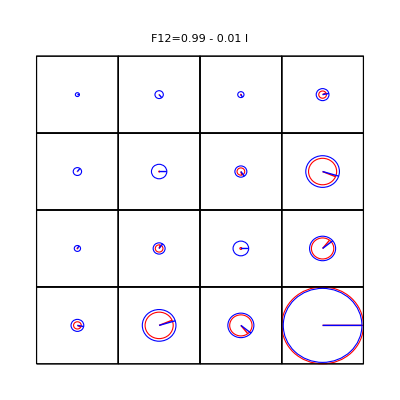
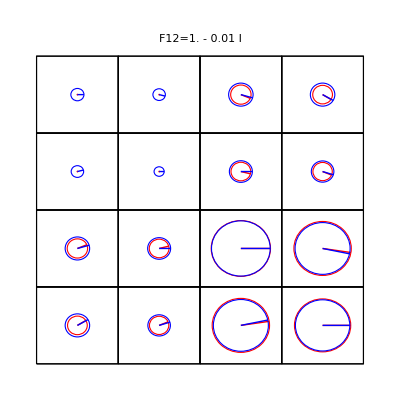
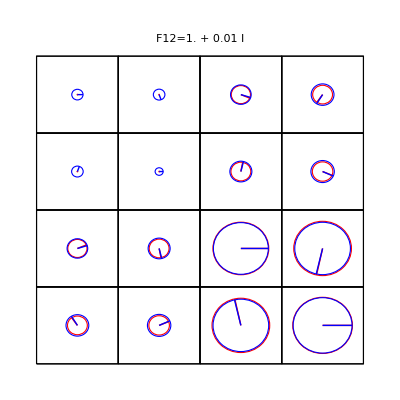
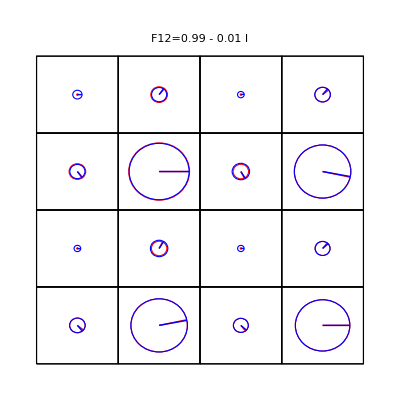
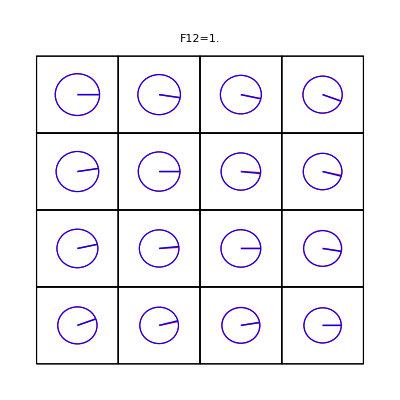
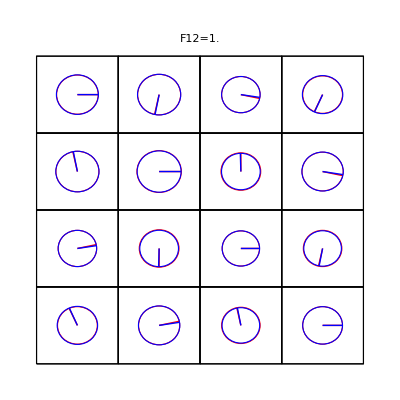
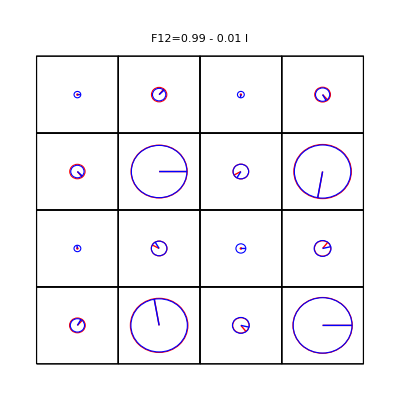
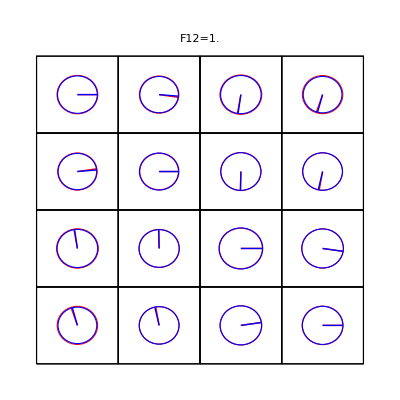
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
set=MapThread[#1->#2&,{params,set7}]; (*best fitting prep and tomo error parameters*)
opE2b1=opE2b/.set; (*calculated measurement operators with tomo errors only*)
ρListInE1=ρListInE/.set;  (*calculated inputρ's with prep errors only*)
pauliSetError1[ρMi_]:=Tr[ρMi.#]&/@opE2b1
pauliSetInErrorL1=pauliSetInErrorL/.set; (*calculated input Pauli sets with both prep and tomo errors*)
ρListInThTomoErr1=ρFromPauliSet/@pauliSetInErrorL1; (*calculated input ρ's with both prep and tomo errors*)
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρListInThTomoErr1,ρInListExp3}]
```

```mathematica
params
((set7 /π 180*10)//Round)/10.
```

{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

{-1.2,-2.8,3.2,3.8,-6.2,-3.,6.5,-3.9,12.4,4.7,0.9,-2.1,-11.6,-10.4}

So errors consisting in
	-1° and -3° for a preparation X(π) pulse on qubit 1 and 2, respectively
	3° and 4° for a preparation -X(π/2) pulse on qubit 1 and 2, respectively
	-6° and -3° for a preparation Y(π/2) pulse on qubit 1 and 2, respectively
	-6.5° and -4° for a tomographic X(π/2) pulse on qubit 1 and 2, respectively
	12.5° and 5° for a tomographic -Y(π/2) pulse on qubit 1 and 2, respectively
	91° and 88° between x1, y1 and x2,y2, respectively
	tomographic frames rotated by -11° with respect to preparation frame ??? 
		fit very well the errors on ρListInExp3.